## Projectile motion in air with and without correction to the air density.

### With Density Correction

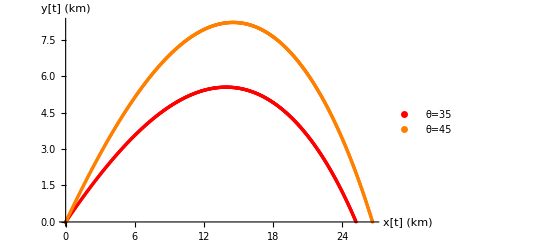

```mathematica
(*Initial Values*)
dt=0.1;ts=0.;tf=100.;v0=700.;BoverM=4.*10^-5;g=9.8;y0=1.*10^4;
(*For example*)
θ=Pi/180.*{35.,45.};
(*Number of theta elements and arrangments; Each one will contain lists as elements and the number of those inner lists = Length[θ]*)
tL=Range[ts,tf,dt];
Vtxall=Table[Table[If[i==1,v0 Cos[θ[[j]]],0],{i,Length[tL]}],{j,1,Length[θ]}]; (*Initializing*)
Vtyall=Table[Table[If[i==1,v0 Sin[θ[[j]]],0],{i,Length[tL]}],{j,1,Length[θ]}];
xtall=Table[Table[0,{i,Length[tL]}],{j,1,Length[θ]}];
ytall=Table[Table[0,{i,Length[tL]}],{j,1,Length[θ]}];
(*Calculations*)
For[j=1,j<= Length[θ],j++,For[i=1,i<Length[tL],i++,vi=√((Vtxall[[j]][[i]])^2+(Vtyall[[j]][[i]])^2);Vtxall[[j]][[i+1]]=Vtxall[[j]][[i]]-(E^(-ytall[[j]][[i]]/y0))BoverM*vi*Vtxall[[j]][[i]]*dt;Vtyall[[j]][[i+1]]=Vtyall[[j]][[i]]-(g dt+(E^(-ytall[[j]][[i]]/y0))BoverM*vi*Vtyall[[j]][[i]]*dt);xtall[[j]][[i+1]]=xtall[[j]][[i]]+Vtxall[[j]][[i]]dt;ytall[[j]][[i+1]]=ytall[[j]][[i]]+Vtyall[[j]][[i]]dt]];
(*Pairs to plot, we divide by 1000 to get distances in km*)
xandy1=Table[If[ytall[[1,i]]/1000.<=-0.01,{0,0},{xtall[[1,i]],ytall[[1,i]]}],{i,1,Length[tL]}];(*If condition to aviod going below y=0*)
xandy2=Table[If[ytall[[2,i]]/1000.<=-0.01,{0,0},{xtall[[2,i]],ytall[[2,i]]}],{i,1,Length[tL]}];
(*Plotting All*)
F1=ListPlot[xandy1/1000.,PlotStyle->{Red,PointSize[0.006]},PlotLegends->{"θ=35"}];
F2=ListPlot[xandy2/1000.,PlotStyle->{Orange,PointSize[0.006]},PlotLegends->{"θ=45"}];
Show[F1,F2,PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"x[t] (km)","y[t] (km)"}]
```

### Without correction

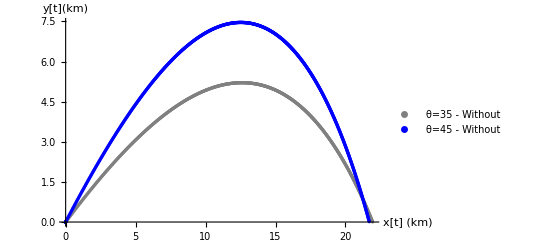

```mathematica
(*Same initial conditions, but we save in different lists to combine all at the end.*)
Vtxall2=Table[Table[If[i==1,v0 Cos[θ[[j]]],0],{i,Length[tL]}],{j,1,Length[θ]}];
Vtyall2=Table[Table[If[i==1,v0 Sin[θ[[j]]],0],{i,Length[tL]}],{j,1,Length[θ]}];
xtall2=Table[Table[0,{i,Length[tL]}],{j,1,Length[θ]}];
ytall2=Table[Table[0,{i,Length[tL]}],{j,1,Length[θ]}];
(*Calculations*)
For[j=1,j<= Length[θ],j++,For[i=1,i<Length[tL],i++,vi=√((Vtxall2[[j]][[i]])^2+(Vtyall2[[j]][[i]])^2);Vtxall2[[j]][[i+1]]=Vtxall2[[j]][[i]]-BoverM*vi*Vtxall2[[j]][[i]]*dt;Vtyall2[[j]][[i+1]]=Vtyall2[[j]][[i]]-(g dt+BoverM*vi*Vtyall2[[j]][[i]]*dt);xtall2[[j]][[i+1]]=xtall2[[j]][[i]]+Vtxall2[[j]][[i]]dt;ytall2[[j]][[i+1]]=ytall2[[j]][[i]]+Vtyall2[[j]][[i]]dt]];
(*Pairs to plot*)
xandy3=Table[If[ytall2[[1,i]]/1000.<=-0.01,{0,0},{xtall2[[1,i]],ytall2[[1,i]]}],{i,1,Length[tL]}];
xandy4=Table[If[ytall2[[2,i]]/1000.<=-0.01,{0,0},{xtall2[[2,i]],ytall2[[2,i]]}],{i,1,Length[tL]}];
(*Plotting All*)
F3=ListPlot[xandy3/1000.,PlotStyle->{Gray,PointSize[0.006]},PlotLegends->{"θ=35 - Without"}];
F4=ListPlot[xandy4/1000.,PlotStyle->{Blue,PointSize[0.006]},PlotLegends->{"θ=45 - Without"}];
Show[F3,F4,PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"x[t] (km)","y[t](km)"}]
```

### Combining Both (With and Without Density Correction)

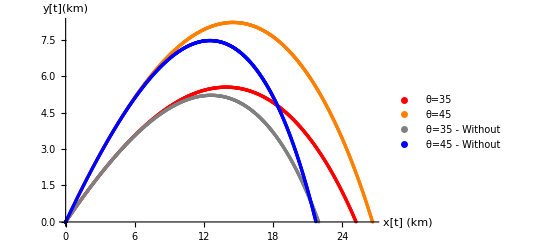

```mathematica
Show[F1,F2,F3,F4,PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"x[t] (km)","y[t](km)"}]
```

### Maximum Range with density correction

```mathematica
θL=Pi/180*Range[20,60,1]; (*We start with several thetas and look for the one that gives maximum range.*)
tL=Range[ts,tf,dt];
Vtxall4=Table[Table[If[i==1,v0 Cos[θL[[j]]],0],{i,Length[tL]}],{j,1,Length[θL]}];
Vtyall4=Table[Table[If[i==1,v0 Sin[θL[[j]]],0],{i,Length[tL]}],{j,1,Length[θL]}];
xtall4=Table[Table[0,{i,Length[tL]}],{j,1,Length[θL]}];
ytall4=Table[Table[0,{i,Length[tL]}],{j,1,Length[θL]}];
(*Calculations*)
For[j=1,j<= Length[θL],j++,For[i=1,i<Length[tL],i++,vi=√((Vtxall4[[j]][[i]])^2+(Vtyall4[[j]][[i]])^2);Vtxall4[[j]][[i+1]]=Vtxall4[[j]][[i]]-(E^(-ytall4[[j]][[i]]/y0))BoverM*vi*(Vtxall4[[j]][[i]])*dt;Vtyall4[[j]][[i+1]]=Vtyall4[[j]][[i]]-(g dt+(E^(-ytall4[[j]][[i]]/y0))BoverM*vi*Vtyall4[[j]][[i]]*dt);xtall4[[j]][[i+1]]=xtall4[[j]][[i]]+Vtxall4[[j]][[i]]dt;ytall4[[j]][[i+1]]=ytall4[[j]][[i]]+Vtyall4[[j]][[i]]dt]];
(*Getting range for each angle*)
xandθ=Table[0,{i,Length[θL]}];
For[j=1,j<= Length[θL],j++,For[i=1,i<Length[tL],i++,If[ytall4[[j]][[i+1]]<=0&&xandθ[[j]]==0,xandθ[[j]]={Interpolation[{{ytall4[[j]][[i]],xtall4[[j]][[i]]},{ytall4[[j]][[i+1]],xtall4[[j]][[i+1]]}},0],θL[[j]]}]]];
(*{Xrange,θ} - Reversed pairs to use interpolate as suggested in the text*)
xandθ ;(*Several ranges for all angles*)
Print["Maximum Range in meters= ",Max[xandθ]] (*Largest Range*)
Print["Maximum Range initial angle in degress= ",(N@180.)/Pi xandθ[[Position[xandθ,Max[xandθ]][[1,1]],-1]] ](*The angle at which it occurs ±1 Degree*)
```

Maximum Range in meters= 26621.8

Maximum Range initial angle in degress= 46.